```mathematica
This notebook contains the code  used to produce the figures reported in 
"Role of body temperature variations in bats immune response to viral infections"
M. R. Fumagalli, S. Zapperi, C. A. M. La Porta
```

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
ClearAll[aA,bA,cA,dA,aS,bS,cS,dS, n, mS, mA, pars, n];
```

```mathematica
totalDays=60;
AvgAmountAI={};
AvgAmountAV={};
AvgFracAI={};
AvgFracAV={};
listFractimeI={};
listFractimeV={};
listAmountI={};
listAmountV={};
InitConditAwakeAll={{0,0}};

Hlist={0,2,4,6,8,10,12,14,16,18,20,22,24};  (*# List values of t_night*)
Jlist={0.2, 0.3,0.4,0.5,0.6,0.7,0.8,0.9};            (*# List values of alpha*)
maxparJ=Length[Jlist]+1;
maxparH=Length[Hlist]+1;
pars=Jlist;
```

```mathematica
For[H=1,H<maxparH,H++,(*Print[H];*)
AvgAmountI={};
AvgAmountV={};
  AvgFracI={};
  AvgFracV={};
  InitConditAwakeAll={{0,0}};
For[J=1,J<maxparJ,J++,(*Print[J];*)

(* SET PARAMETERS *)
(* c=\gamma/\beta *)
aA=1.5;
dA=0.15;
cA=1;
bA=1;
mA=0.15;

aS=aA*N[Jlist[[J]]];
dS=0.15;
cS=1;
bS=1;
mS=0.15;

tawake=N[Hlist[[H]]];
tsleep=24-tawake;

(***** COMMENT/UNCOMMENT TE FOLLOWING LINES TO SWTCH FROM LYTIC TO NON-LYTIC MDEL *****)
(* Lytic model *)
Eqat = {
Derivative[1][Virus][t] == Virus[t]*(a-m) -b*Immune[t]*Virus[t] ,
    Derivative[1][Immune][t] == -d*Immune[t]+b*c Virus[t] 
}; 

InitCondit0= {(a-m)/b, (d*(a-m))/((b*b)*c)}/.a->aS/.b->bS/.c->cS/.d->dS/.m->mS;
InitConditAwake = { (a-m)/b, (d*(a-m))/((b*b)*c)}/.a->aA/.b->bA/.c->cA/.d->dA/.m->mA;
(* Non Lytic model *)
(*EqatNL = {
Derivative[1][Virus][t] == Virus[t]*(a/(1+b*Immune[t]) - m*Virus[t] ,
    Derivative[1][Immune][t] == -d*Immune[t]+b*c Virus[t] 
};
InitConditSleep= { (a-m)/(b*m),(d*(a-m))/((b*b)*m*c)}/.a->aS/.b->bS/.c->cS/.d->dS/.m->mS;
InitConditAwake = { (a-m)/(b*m),(d*(a-m))/((b*b)*m*c)}/.a->aA/.b->bA/.c->cA/.d->dA/.m->mA;
*) 


InitConditFOR= {Immune[0] == I0, Virus[0] == V0};

n=0;
ttot={0};	
For[n=0,n<totalDays*2,n++,
	    If[n==0,
			IC=InitConditFOR/.I0-> InitCondit0 [[1]]/.V0-> InitCondit0 [[2]]; 
				TransPoint={{IC[[2]][[2]],IC[[1]][[2]]}};,
			IC=InitConditFOR/.I0-> ifuns[[2]][[0]][tm]/.V0-> ifuns[[1]][[0]][tm]; 
				AppendTo[TransPoint,{IC[[2]][[2]],IC[[1]][[2]]}] ;
	];				  
	If[tawake<24,  
	   If[Mod[n,2]==0,
			eq=Eqat/.a->aA/.b->bA/.c->cA/.d->dA/. m->mA; tm=tawake; AppendTo[ttot,ttot[[-1]]+tawake],
			eq=Eqat/.a->aS/.b->bS/.c->cS/.d->dS/. m->mS; tm=tsleep ; AppendTo[ttot,ttot[[-1]]+tsleep]
	],
          eq=Eqat/.a->aA/.b->bA/.c->cA/.d->dA/. m->mA; tm=12; AppendTo[ttot,ttot[[-1]]+12]];
	
	MergedSysFOR=Join[eq,IC];
	mysolFOR=NDSolve[MergedSysFOR,
	         	{Virus[t],Immune[t]},
			{t,0,tm}
			];
	ifuns=First[{Virus[t],Immune[t]}/.mysolFOR] ;

	If[n==0,
	VirusData=Part[ifuns,1,0]["ValuesOnGrid"];ImmuneData=Part[ifuns,2,0]["ValuesOnGrid"]; ,
	VirusData=Flatten[Append[VirusData,Part[ifuns,1,0]["ValuesOnGrid"]]]; 
ImmuneData=Flatten[Append[ImmuneData,Part[ifuns,2,0]["ValuesOnGrid"]]]; 
	];
	If[n==0,
	VirusData2= Flatten[Table[Virus[t]/.mysolFOR, {t,0,tm,1./60}]];
	ImmuneData2= Flatten[Table[Immune[t]/.mysolFOR, {t,0,tm,1./60}]]; ,
	VirusData2=Flatten[Append[VirusData2, Table[Virus[t]/.mysolFOR, {t,1./60,tm,1./60}]]];
	ImmuneData2=Flatten[Append[ImmuneData2, Table[Immune[t]/.mysolFOR, {t,1./60,tm,1./60}]]]; 
	];
];
Final=InitConditFOR/.I0-> ifuns[[2]][[0]][tm]/.V0-> ifuns[[1]][[0]][tm]; 
AppendTo[TransPoint,{Final[[2]][[2]],Final[[1]][[2]]}] ;
ttot2=Range[0,ttot[[-1]],1./60];

FractimeV={};
       AmountV={};
FractimeI={}; 
       AmountI={};


(*Take the data of value of virus in time, and for each day calculate fraction of timepoints below InitConditAwake. Transient neglected*);
For[k=50,k<totalDays,k++,
FractimeI=Append[FractimeI,Length[Select[ImmuneData2[[1+(60*24*(k-1));;1+(60*24*k)]],#<InitConditAwake[[1]]&]]/1440.];
FractimeV=Append[FractimeV,Length[Select[VirusData2[[1+(60*24*(k-1));;1+(60*24*k)]],#<InitConditAwake[[2]]&]]/1440.];
];

AvgFracI=Append[AvgFracI,{tawake,N[Jlist[[J]]],Mean[FractimeI]}];
AvgFracV=Append[AvgFracV,{tawake,N[Jlist[[J]]],Mean[FractimeV]}];

(*Take the data of value of virus in time, and for each day calculate average. *);
For[k=50,k<totalDays,k++,
AmountI=Append[AmountI,Mean[ImmuneData2[[1+(60*24*(k-1));;1+(60*24*k)]]/InitConditAwake[[1]]]];
AmountV=Append[AmountV,Mean[VirusData2[[1+(60*24*(k-1));;1+(60*24*k)]]/InitConditAwake[[2]]]];
];

	AvgAmountI=Append[AvgAmountI,{tawake,N[Jlist[[J]]],Mean[AmountI]}];
	AvgAmountV=Append[AvgAmountV,{tawake,N[Jlist[[J]]],Mean[AmountV]}];
	InitConditAwakeAll=Append[InitConditAwakeAll,InitConditAwake];

(* Flat to arbitrary precision *)
listFractimeI=Append[listFractimeI,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[FractimeI*100.]]}];
listFractimeV=Append[listFractimeV,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[FractimeV*100.]]}];
listAmountI=Append[listAmountI,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[AmountI*100.]]}];
listAmountV=Append[listAmountV,{tawake,N[Jlist[[J]]],DeleteDuplicates[Floor[AmountV*100.]]}];
];

For[i=1,i<maxparJ,i++,
AvgAmountAI=Append[AvgAmountAI,AvgAmountI[[i]]]; 
AvgAmountAV=Append[AvgAmountAV,AvgAmountV[[i]]];
  AvgFracAI=Append[AvgFracAI,AvgFracI[[i]]];
  AvgFracAV=Append[AvgFracAV,AvgFracV[[i]]];
];

]
```

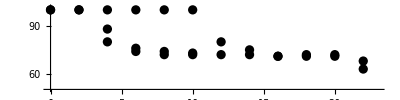

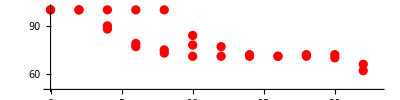

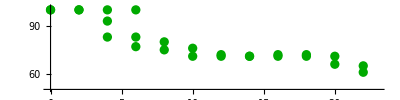

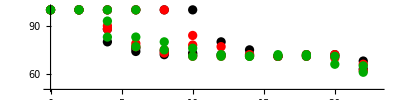

```mathematica
T102=Table[{listFractimeI[[1;;;;4]][[i]][[1]],listFractimeI[[1;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T202=Table[{listFractimeI[[1;;;;4]][[i]][[1]],
			If[Length[listFractimeI[[1;;;;4]][[i]][[3]]]>1,listFractimeI[[1;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T104=Table[{listFractimeI[[2;;;;4]][[i]][[1]],listFractimeI[[2;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T204=Table[{listFractimeI[[2;;;;4]][[i]][[1]],
			If[Length[listFractimeI[[2;;;;4]][[i]][[3]]]>1,listFractimeI[[2;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T106=Table[{listFractimeI[[3;;;;4]][[i]][[1]],listFractimeI[[3;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeI[[1;;;;4]]]} ];
T206=Table[{listFractimeI[[3;;;;4]][[i]][[1]],
			If[Length[listFractimeI[[3;;;;4]][[i]][[3]]]>1,listFractimeI[[3;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeI[[1;;;;4]]]} ];

P1=ListPlot[{T102,T202}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Black}, AspectRatio->0.25]
P2=ListPlot[{T104,T204}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Red}, AspectRatio->0.25]
P3=ListPlot[{T106,T206}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Darker[Green]}, AspectRatio->0.25]
Show[P1,P2,P3]
```

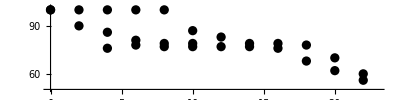

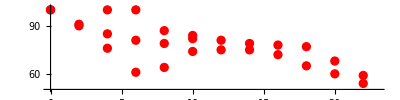

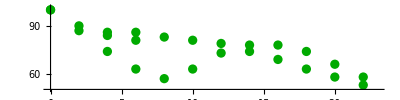

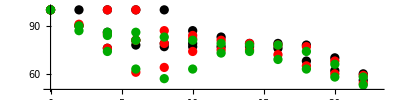

```mathematica
T102V=Table[{listFractimeV[[1;;;;4]][[i]][[1]],listFractimeV[[1;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T202V=Table[{listFractimeV[[1;;;;4]][[i]][[1]],
			If[Length[listFractimeV[[1;;;;4]][[i]][[3]]]>1,listFractimeV[[1;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T104V=Table[{listFractimeV[[2;;;;4]][[i]][[1]],listFractimeV[[2;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T204V=Table[{listFractimeV[[2;;;;4]][[i]][[1]],
			If[Length[listFractimeV[[2;;;;4]][[i]][[3]]]>1,listFractimeV[[2;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T106V=Table[{listFractimeV[[3;;;;4]][[i]][[1]],listFractimeV[[3;;;;4]][[i]][[3]][[1]]}, {i,1,Length[listFractimeV[[1;;;;4]]]} ];
T206V=Table[{listFractimeV[[3;;;;4]][[i]][[1]],
			If[Length[listFractimeV[[3;;;;4]][[i]][[3]]]>1,listFractimeV[[3;;;;4]][[i]][[3]][[2]],-1]},  {i,1,Length[listFractimeV[[1;;;;4]]]} ];

P1=ListPlot[{T102V,T202V}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Black}, AspectRatio->0.25]
P2=ListPlot[{T104V,T204V}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Red}, AspectRatio->0.25]
P3=ListPlot[{T106V,T206V}, PlotRange->{{0,23},{50,102}}, PlotStyle->{Darker[Green]}, AspectRatio->0.25]
Show[P1,P2,P3]
```

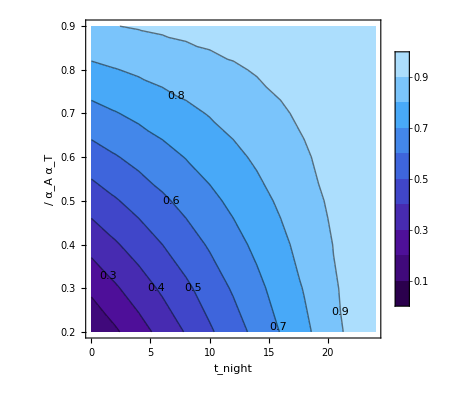

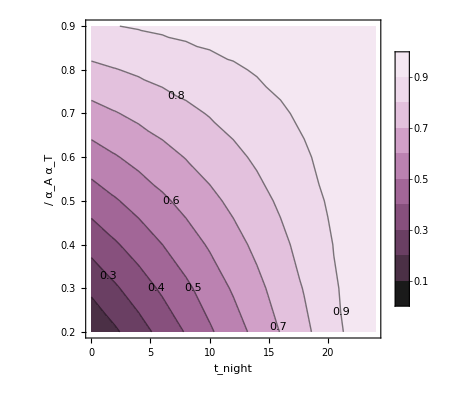

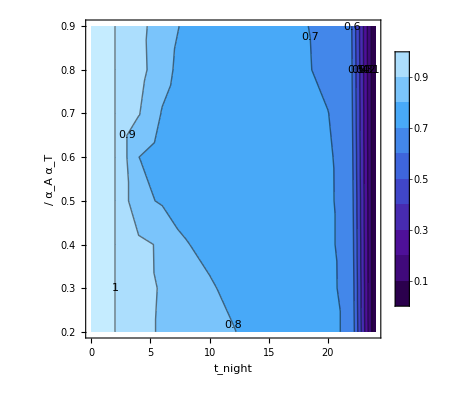

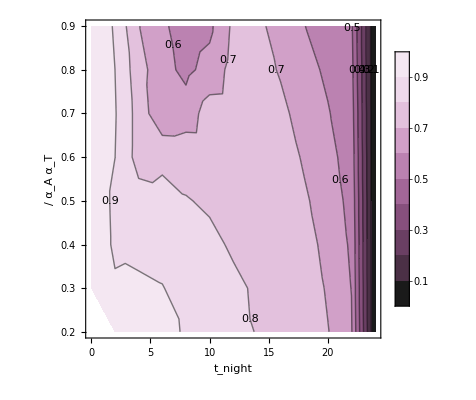

```mathematica
ListContourPlot[AvgAmountAI, 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","T"]"/"Subscript["α","A"]},{Subscript["t","night"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"DeepSeaColors",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1},
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
AspectRatio->1, 
ContourLabels->True,
PlotLegends->Automatic
]

ListContourPlot[AvgAmountAV, 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","T"]"/"Subscript["α","A"]},{Subscript["t","night"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"FuchsiaTones",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1}, 
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
AspectRatio->1, 
ContourLabels->True,
PlotLegends->Automatic
]

ListContourPlot[Floor[AvgFracAI*1000.]/1000., 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","T"]"/"Subscript["α","A"]},{Subscript["t","night"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"DeepSeaColors",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1}, (*{{0,24},{0,2}},*)
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
AspectRatio->1, 
ContourLabels->True,
PlotLegends->Automatic
]


ListContourPlot[AvgFracAV, 
Axes->False,
Frame->True,FrameLabel->{{Subscript["α","T"]"/"Subscript["α","A"]},{Subscript["t","night"]}},
RotateLabel->True, 
ColorFunction->ColorData[{"FuchsiaTones",{0,1}}],
ColorFunctionScaling->False,
PlotRange->{0,1}, (*{{0,24},{0,2}},*)
 LabelStyle->{Directive[Black,22],FontFamily->"Times"},
InterpolationOrder->10,
PlotLegends->Automatic,
AspectRatio->1 ,
(*PlotLegends->Placed[LineLegend[{{Red,Dashed},Red},{Subscript["v","eq"],Subscript["I","eq"]}], { Right,Top}]*)
ContourLabels->True]
```

```mathematica
(*****************************************)
(************   Trajectory    ***********)
(*****************************************)
```

```mathematica
ClearAll[aA,bA,cA,dA,aS,bS,cS,dS, n, mS, mA, pars, n];
(* c=\gamma /b *)
```

```mathematica
totalDays=10;
aA=1.5;
dA=0.15;
cA=1;
bA=1;
mA=0.15;

aS=0.4;
dS=0.15;
cS=1;
bS=1;
mS=0.15;

tawake=8;
tsleep=24-tawake;

(* Lytic model *)
Eqat = {
Derivative[1][Virus][t] == Virus[t]*(a-m) -b*Immune[t]*Virus[t] ,
    Derivative[1][Immune][t] == -d*Immune[t]+b*c Virus[t] 
}; 

InitCondit0= {(a-m)/b, (d*(a-m))/((b*b)*c)}/.a->aS/.b->bS/.c->cS/.d->dS/.m->mS;
InitConditAwake = { (a-m)/b, (d*(a-m))/((b*b)*c)}/.a->aA/.b->bA/.c->cA/.d->dA/.m->mA;
(* Non Lytic model *)
(*Eqat={
Derivative[1][Virus][t] == Virus[t]*(a/(1+b*Immune[t])) - m*Virus[t] ,
    Derivative[1][Immune][t] == -d*Immune[t]+b*c Virus[t] 
};
InitConditSleep= { (a-m)/(b*m),(d*(a-m))/((b*b)*m*c)}/.a->aS/.b->bS/.c->cS/.d->dS/.m->mS;
InitConditAwake = { (a-m)/(b*m),(d*(a-m))/((b*b)*m*c)}/.a->aA/.b->bA/.c->cA/.d->dA/.m->mA;
*)


InitConditFOR= {Immune[0] == I0, Virus[0] == V0};

n=0;
ttot={0};	
For[n=0,n<totalDays*2,n++,
	    If[n==0,
			IC=InitConditFOR/.I0-> InitCondit0 [[1]]/.V0-> InitCondit0 [[2]]; 
				TransPoint={{IC[[2]][[2]],IC[[1]][[2]]}};,
			IC=InitConditFOR/.I0-> ifuns[[2]][[0]][tm]/.V0-> ifuns[[1]][[0]][tm]; 
				AppendTo[TransPoint,{IC[[2]][[2]],IC[[1]][[2]]}] ;
	];				  
	  
	   If[Mod[n,2]==0,
			eq=Eqat/.a->aA/.b->bA/.c->cA/.d->dA/. m->mA; tm=tawake; AppendTo[ttot,ttot[[-1]]+tawake],
			eq=Eqat/.a->aS/.b->bS/.c->cS/.d->dS/. m->mS; tm=tsleep ; AppendTo[ttot,ttot[[-1]]+tsleep]
	];          
	
	MergedSysFOR=Join[eq,IC];
	mysolFOR=NDSolve[MergedSysFOR,
	         	{Virus[t],Immune[t]},
			{t,0,tm}
			];
	ifuns=First[{Virus[t],Immune[t]}/.mysolFOR] ;

	If[n==0,
	VirusData=Part[ifuns,1,0]["ValuesOnGrid"];ImmuneData=Part[ifuns,2,0]["ValuesOnGrid"]; ,
	VirusData=Flatten[Append[VirusData,Part[ifuns,1,0]["ValuesOnGrid"]]]; 
ImmuneData=Flatten[Append[ImmuneData,Part[ifuns,2,0]["ValuesOnGrid"]]]; 
	];
	If[n==0,
	VirusData2= Flatten[Table[Virus[t]/.mysolFOR, {t,0,tm,1./60}]];
	ImmuneData2= Flatten[Table[Immune[t]/.mysolFOR, {t,0,tm,1./60}]]; ,
	VirusData2=Flatten[Append[VirusData2, Table[Virus[t]/.mysolFOR, {t,1./60,tm,1./60}]]];
	ImmuneData2=Flatten[Append[ImmuneData2, Table[Immune[t]/.mysolFOR, {t,1./60,tm,1./60}]]]; 
	];
];
Final=InitConditFOR/.I0-> ifuns[[2]][[0]][tm]/.V0-> ifuns[[1]][[0]][tm]; 
AppendTo[TransPoint,{Final[[2]][[2]],Final[[1]][[2]]}] ;
ttot2=Range[0,ttot[[-1]],1./60];
```

```mathematica
MaxVirus=Max[N[IntegerPart[Max[VirusData]*12]/10],InitConditAwake[[2]]];
MaxImmune=Max[N[IntegerPart[Max[ImmuneData]*12]/10],InitConditAwake[[1]]];
MinVirus=N[IntegerPart[Min[VirusData]-0.1]];
MinImmune=N[IntegerPart[Min[ImmuneData]-0.1]];
```

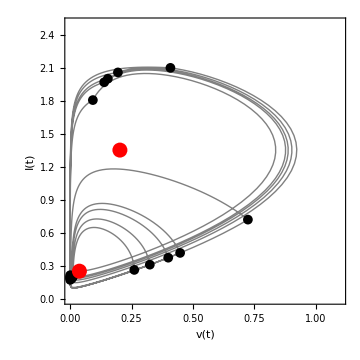

```mathematica
L1=ListLinePlot[Transpose[{VirusData,ImmuneData}],
	 AlignmentPoint->Center,
	Axes->False,Frame->True,FrameLabel->Join[{"v(t)","I(t)"},{None,None}],RotateLabel->True,
	Ticks->{Table[j,{j,0,MaxVirus,(MaxVirus)/5}],Table[j,{j,0, MaxImmune,MaxImmune/5}]},
	PlotStyle->{Directive[Gray,Thick]},
	PlotRange->{{0,MaxVirus},{0,MaxImmune}},
	PlotRangePadding->Scaled[.05],
	LabelStyle->{Directive[Black,22],FontFamily->"Times"},AspectRatio->1
	];
L2=ListPlot[TransPoint, PlotStyle->Directive[Large, Black],Axes->False,Frame->True,FrameLabel->Join[{"v(t)","I(t)"},{None,None}],RotateLabel->True, PlotRange->All,PlotRangePadding->0.1, LabelStyle->{Directive[Black,22],FontFamily->"Times"}, PlotStyle->{Directive[Gray,Thick]},  AspectRatio->1];
Leq=ListPlot[{Reverse[InitCondit0],Reverse[InitConditAwake]},PlotStyle->{PointSize[0.03],Red}];
Show[L1,L2, Leq]
```

```mathematica
L3=ListLinePlot[TemporalData[{VirusData2,ImmuneData2}, {ttot2}],
	 AlignmentPoint->Center,
	ImageSize->Large,
	AspectRatio->0.5,
	Axes->True,
	AxesLabel->{"Virus","Immune"}
  PlotRange->{{0,All},{0,All}},
	Frame->True,FrameStyle->Directive[10],FrameLabel->{{Style["Concentration",18],None},{Style["Time [h]",18], None}},
	LabelStyle->{Directive[Black,22],FontFamily->"Times"},
	PlotStyle->{Directive[Purple,Thick,Dashed],Directive[Blue,Thick]},
	FrameTicksStyle->Directive[Black,18],PlotLegends->Placed[LineLegend[{Directive[Purple,Thick,Dashed],Directive[Blue,Thick]},{"v(t)","I(t)"}], { Right,Top}]	
	(*{FontFamily->"Arial",FontSize->18,Black}*)
	];
L4=ListPlot[TemporalData[TransPoint, {ttot}], PlotStyle->{Directive[Purple,Large],Directive[Blue,Large]}];
(*L4V2=ListPlot[TemporalData[TransPoint, {ttot}], PlotStyle->{Directive[Purple,Large],Directive[White,Large]}];
L4V=ListPlot[TemporalData[Transpose[TransPoint][[1]], {ttot}], PlotStyle->{Directive[Purple,Large]}, PlotRange->{{0,All},{0,All}}];
L4I=ListPlot[TemporalData[Transpose[TransPoint][[2]], {ttot}], PlotStyle->{Directive[Blue,Large]}];*)
```

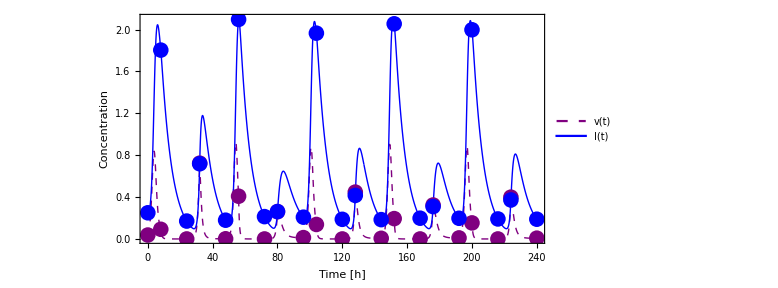

```mathematica
Show[L3,L4]
```